```mathematica
(*Задаём параметры тора*)
R=2
r=1

(*Метод 1: Неявное*)
torusImplicit=ContourPlot3D[(x^2+y^2+z^2+R^2-r^2)^2-4 R^2 (x^2+y^2)==0,{x,-3,3},{y,-3,3},{z,-2,2},ColorFunction->"NeonColors",Axes->True,Boxed->False,PlotLabel->"Тор: ContourPlot3D"];

(*Метод 2: Параметрическое*)
torusParametric=ParametricPlot3D[{(R+r Cos[u]) Cos[v],(R+r Cos[u]) Sin[v],r Sin[u]},{u,0,2 Pi},{v,0,2 Pi},ColorFunction->"NeonColors",Axes->True,Boxed->False,PlotLabel->"Тор: ParametricPlot3D"];

(*Метод 3: Явное*)
torusExplicit=RevolutionPlot3D[{R+r Cos[u],r Sin[u]},{u,0,2 Pi},RevolutionAxis->{0,0,1},ColorFunction->"NeonColors",Axes->True,Boxed->False,PlotLabel->"Тор: RevolutionPlot3D"];

GraphicsRow[{torusImplicit,torusParametric,torusExplicit},ImageSize->Large]
```

2

1

-Graphics-

```mathematica
(*1195 Филлипова*)

solPDE=NDSolveValue[{x*D[z[x,y],x]-2*y*D[z[x,y],y]==x^2+y^2,z[x,1]==x^2},z,{x,-2,2},{y,0.5,2}]

srf=Plot3D[solPDE[x,y],{x,-2,2},{y,0.5,2},PlotRange->All,ColorFunction->(ColorData["NeonColors"][#3]&),AxesLabel->{"x","y","z"},PlotLabel->"Решённая поверхность (x zₓ - 2 y zᵧ = x.b2 + y.b2)"];

curve=ParametricPlot3D[{x,1,x^2},{x,-2,2},PlotStyle->{Thick,Cyan}];

Show[srf,curve,ImageSize->Large]
```

NDSolveValue::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

InterpolatingFunction[…]

-Graphics3D-

Общее решение (система 789):

{{x→({t}↦2 ⅇ^(2 t) sin(t)+1 ⅇ^(2 t) (cos(t)-sin(t))),y→({t}↦2 ⅇ^(2 t) (sin(t)+cos(t))-2 1 ⅇ^(2 t) sin(t))}}

Общее решение (система 811):

{{x→({t}↦1 ⅇ^t (t+1)-2 ⅇ^t t-3 ⅇ^t t),y→({t}↦2 1 ⅇ^t t-2 ⅇ^t (2 t-1)-2 3 ⅇ^t t),z→({t}↦1 (-ⅇ^t) t+2 ⅇ^t t+3 ⅇ^t (t+1))}}

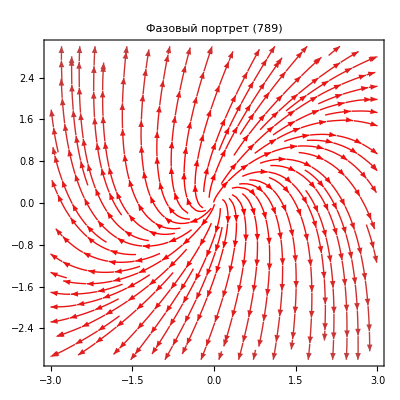

```mathematica
(*789 Филлипова*)
sol789=DSolve[{x'[t]==x[t]+y[t],y'[t]==-2 x[t]+3 y[t]},{x,y},t];

Print["Общее решение (система 789):"];
Print[sol789//TraditionalForm];

neonColorFunction2D=Function[{x,y,u,v},Blend[{Red,Cyan, White},Rescale[Norm[{u,v}],{0,7}]]];

neonColorFunction3D=Function[{xx,yy,zz,vx,vy,vz,speed},ColorData["NeonColors"][speed]];

phasePlot789=StreamPlot[{x+y,-2 x+3 y},{x,-3,3},{y,-3,3},StreamStyle->Thick,StreamColorFunction->neonColorFunction2D,StreamColorFunctionScaling->False,PlotRange->All,Axes->True,PlotLabel->"Фазовый портрет (789)"];

(*811 Филлипова*)
sol811=DSolve[{x'[t]==2 x[t]-y[t]-z[t],y'[t]==2 x[t]-y[t]-2 z[t],z'[t]==2 z[t]-x[t]+y[t]},{x,y,z},t];

Print["Общее решение (система 811):"];
Print[sol811//TraditionalForm];

vectorPlot811=VectorPlot3D[{2 x-y-z,2 x-y-2 z,2 z-x+y},{x,-2,2},{y,-2,2},{z,-2,2},VectorColorFunction->neonColorFunction3D,VectorColorFunctionScaling->True,Axes->True,BoxRatios->{1,1,1},PlotRange->All,PlotLabel->"Фазовый портрет (811)"];

GraphicsRow[{phasePlot789,vectorPlot811},ImageSize->Large]
```

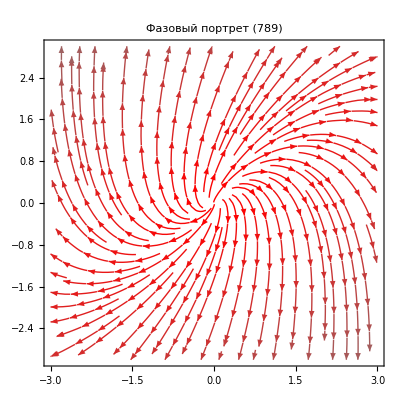

-Graphics-

```mathematica
(*866 Филлипова*)
A={{2,0,-1},{1,-1,0},{3,-1,-1}}
solA=DSolve[{x'[t],y'[t],z'[t]}==A.{x[t],y[t],z[t]},{x,y,z},t];
Print["Общее решение системы x'(t) = A x(t):"];
Print[solA//TraditionalForm];

neonColorFunction3D=Function[{xx,yy,zz,vx,vy,vz,speed},Blend[{Cyan,Black,Red},Rescale[speed,{0,6}]]];

vecPlotA=VectorPlot3D[A.{x,y,z},{x,-2,2},{y,-2,2},{z,-2,2},VectorColorFunction->neonColorFunction3D,VectorColorFunctionScaling->False,BoxRatios->{1,1,1},Axes->True,PlotRange->All,PlotLabel->"Фазовый портрет системы: x'(t) = A x(t)"];

vecPlotA
```

{{2,0,-1},{1,-1,0},{3,-1,-1}}

Общее решение системы x'(t) = A x(t):

{{x→({t}↦(2 t^2)/2+1/2 1 (t^2+4 t+2)+1/2 3 (-t^2-2 t)),y→({t}↦-(3 t^2)/2+1/2 1 (t^2+2 t)+1/2 2 (t^2-2 t+2)),z→({t}↦1 (t^2+3 t)+2 (t^2-t)+3 (-t^2-t+1))}}

-Graphics3D-

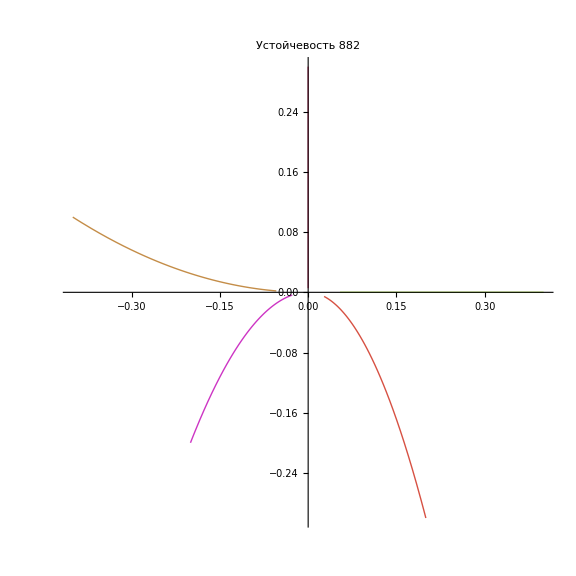

Нулевое решение устойчиво

Нулевое решение не устойчиво

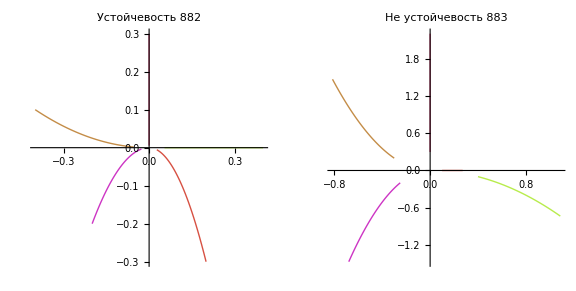

```mathematica
(*882 Филлипова*)
eq882={x'[t]==-x[t],y'[t]==-2 y[t]};

icList882={{x[0]==0.4,y[0]==0.0},{x[0]==-0.4,y[0]==0.1},{x[0]==0.2,y[0]==-0.3},{x[0]==0.0,y[0]==0.3},{x[0]==-0.2,y[0]==-0.2}};

sols882=Table[NDSolve[Join[eq882,ic],{x,y},{t,0,2}],{ic,icList882}];

plot882=ParametricPlot[Evaluate[Table[{x[t],y[t]}/. sols882[[i]],{i,Length[sols882]}]],{t,0,2},PlotRange->All,AspectRatio->1,Axes->True,PlotStyle->Table[{Thick,ColorData["NeonColors"][Rescale[i,{1,Length[sols882]}]]},{i,Length[sols882]}],PlotLabel->"Устойчевость 882"]

Print["Нулевое решение устойчиво"];
(*883 Филлипова*)
eq883={x'[t]==x[t],y'[t]==2 y[t]};

icList883={{x[0]==0.4,y[0]==-0.1},{x[0]==-0.3,y[0]==0.2},{x[0]==0.1,y[0]==0.0},{x[0]==0.0,y[0]==0.3},{x[0]==-0.25,y[0]==-0.2}};

sols883=Table[NDSolve[Join[eq883,ic],{x,y},{t,0,1}],{ic,icList883}];

plot883=ParametricPlot[Evaluate[Table[{x[t],y[t]}/. sols883[[i]],{i,Length[sols883]}]],{t,0,1},PlotRange->All,AspectRatio->1,Axes->True,PlotStyle->Table[{Thick,ColorData["NeonColors"][Rescale[i,{1,Length[sols883]}]]},{i,Length[sols883]}],PlotLabel->"Не устойчевость 883"];

Print["Нулевое решение не устойчиво"];

GraphicsRow[{plot882,plot883},ImageSize->Large]
```